## This is an example of running a C code from Mathematica

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jinyunlin/QFE-Research/affineFlow-2/JintestCode/testing/ConstantLattice

```mathematica
AData=Import["Current/data/CurvedTriangleupdate_16_final.dat"];
BData=Import["Current/data/CurvedTriangleupdate_16_initial.dat"];
(*AData[[1]]
BData[[1]]*)
AData[[All,{3,4,5}]]=AData[[All,{3,4,5}]]/Norm/@(AData[[All,{3,4,5}]]);
BData[[All,{3,4,5}]]=BData[[All,{3,4,5}]]/Norm/@(BData[[All,{3,4,5}]]);
(*AData[[1]]
BData[[1]]*)

Diff=AData-BData;
PlotData=Table[{AData[[All,{3,4,5}]][[i]],Diff[[All,{3,4,5}]][[i]]},{i,Length[AData]}];
makeArrow[{pos_,vec_}]:=Arrow[{pos,pos+vec}];
gr=Graphics3D[{{Red,(*Vector color*)Arrowheads[0.02],(*Size of the arrowheads*)(makeArrow/@PlotData) (*Applying the function to each data point*)},{Blue,PointSize[Medium],Point[PlotData[[All,1]]]}},Boxed->True,Axes->True, ViewPoint->{0,0,1}]
```

-Graphics3D-

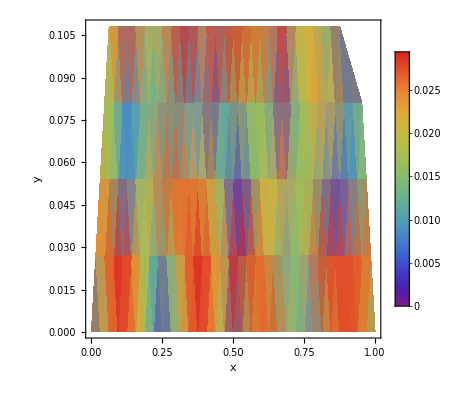

```mathematica
returnFullPos[L_]:=Module[{points,r1,r2},r1={1,0};
r2={1/2,Sqrt[3]/2};
Table[Table[r2*j/L+r1*i/L,{i,0,L-j}],{j,0,L}]]
func=Norm/@Diff[[All, {3,4,5}]];
pos=Flatten[returnFullPos[32],1];
StackedData=Table[Flatten[{pos[[i]],func[[i]]}],{i,Length[func]}];
fig=ListDensityPlot[StackedData,ColorFunction->"Rainbow",PlotLegends->True,FrameLabel->{"x","y"},PlotRange->All]
```

```mathematica
(*AData =  Import["data/CurvedTriangleupdate_32_final.dat"];
BData =  Import["data/CurvedTriangleupdate_128_final.dat"];
{LA, LB} = {32, 128}; 
AData = AData[[All, {3,4,5}]]/LA;
BData = BData[[All, {3,4,5}]]/LB;*)

returnstruct[data_, L_]:=Module[{counter = L, ini=1, arr},
arr= {} ;
Do[AppendTo[arr, data[[ini;;ini+counter]]];
ini+=counter+1; 
counter -=1;
,{i, 1,L}]; 
arr
]
returnPos[L_]:=Module[{points, r1, r2},
r1 = {1,0};
r2={1/2, Sqrt[3]/2};
Table[Table[r2*j/L+r1*i/L,{i, 0, L-j-1}], {j, 0,L-1}]]
returnFullPos[L_]:=Module[{points, r1, r2},
r1 = {1,0};
r2={1/2, Sqrt[3]/2};
Table[Table[r2*j/L+r1*i/L,{i, 0, L-j}], {j, 0,L}]]
```

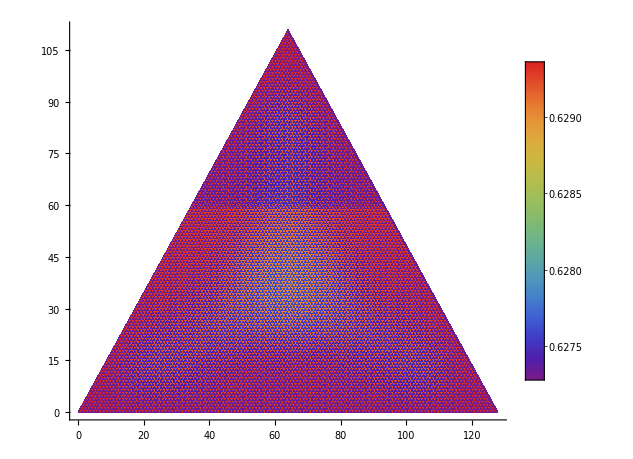

```mathematica
extractRowLinks[arr_]:=Module[{L=Length[arr], start, end},
start = arr[[1;;-2]];
end = arr[[2;;]];
Norm/@(end-start)]
ParseFaceDataold[data_]:=Module[{r1,r2, r3}, 
(*r1 = {1,0};
r2={1/2, Sqrt[3]/2};
r3={0,0};*)
(*Table[Flatten[{data[[i,1]]*r1+r2*data[[i,2]], data[[i, 3]]}],{i, Length[data]}]*)
Table[Flatten[{data[[i,1]]*r1+r2*data[[i,2]], data[[i, 3]]}],{i, Length[data]}]
]
ParseFaceData[data_]:=Module[{func,pos},func=data[[All,7]];
pos=Table[Take[data[[i]],6],{i,Length[data]}];
pos=Partition[#,2]&/@pos;
Table[{pos[[i]],func[[i]]}, {i, Length[pos]}]]
Data = Import["Area.dat", "table"];
res= ParseFaceData[Data];
minValue=Min[res[[All,2]]];
maxValue=Max[res[[All,2]]];
scaledColorFunction[value_]:=ColorData["Rainbow"][(value-minValue)/(maxValue-minValue)];
heatMap=Graphics[{scaledColorFunction[#[[2]]],Polygon[#[[1]]]}&/@res,Axes->True];
legend=BarLegend[{"Rainbow",{minValue,maxValue}}];
Legended[heatMap,legend]
```

```mathematica
Max[ar]
```

0.62936

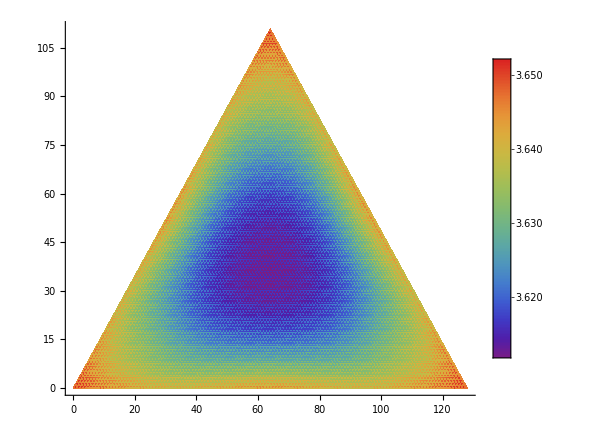

```mathematica
Data = Import["Perimeter.dat", "table"];
res= ParseFaceData[Data];
minValue=Min[res[[All,2]]];
maxValue=Max[res[[All,2]]];
scaledColorFunction[value_]:=ColorData["Rainbow"][(value-minValue)/(maxValue-minValue)];
heatMap=Graphics[{scaledColorFunction[#[[2]]],Polygon[#[[1]]]}&/@res,Axes->True];
legend=BarLegend[{"Rainbow",{minValue,maxValue}}];
Legended[heatMap,legend]
```

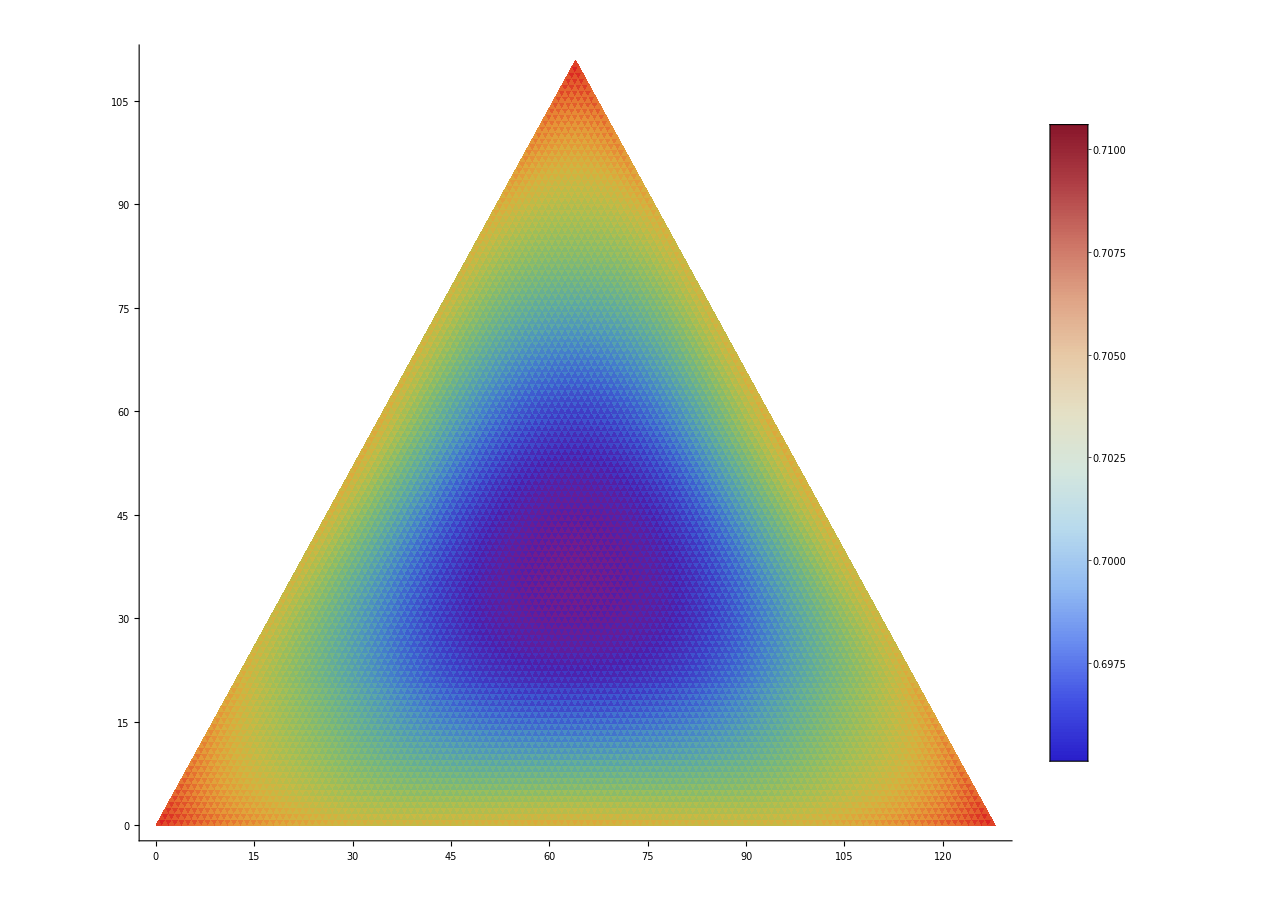

```mathematica
Data = Import["Circumradius.dat", "table"];
res= ParseFaceData[Data];
minValue=Min[res[[All,2]]];
maxValue=Max[res[[All,2]]];
scaledColorFunction[value_]:=ColorData["Rainbow"][(value-minValue)/(maxValue-minValue)];
heatMap=Graphics[{scaledColorFunction[#[[2]]],Polygon[#[[1]]]}&/@res,Axes->True];
legend=BarLegend[{"ThermometerColors",{minValue,maxValue}}];
Legended[heatMap,legend]
```

0.000208624

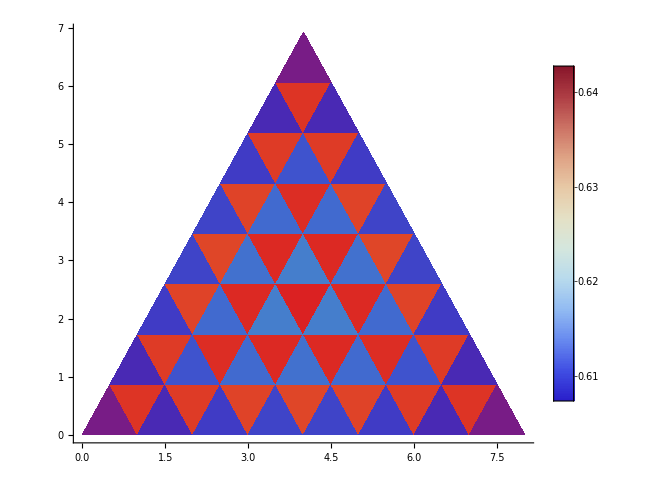

```mathematica
arr = res[[All, 2]];
Mean[arr^2]-Mean[arr]^2
```

```mathematica
(*Data=Import["/Users/jinyunlin/QFE-Research/affineFlow-2/JintestCode/testing/ConstantLattice/Analysis/CurvedTriangleupdate_128_final.dat", "Table"];
Data/=128;
res = returnstruct[Data, 128];
edges = extractRowLinks/@res;
pos = returnPos[128];
Data = Table[Flatten[{Flatten[pos, 1][[i]],Flatten[edges, 1][[i]]}], {i, Length[Flatten[pos, 1]]}]; *)
df = Import["deficitAngle.dat"][[All, {3}]];
dual = Import["dualArr.dat"][[All, {3}]];
Data=df/dual;
pos = returnFullPos[128];
StackedData = Table[Flatten[{Flatten[pos, 1][[i]],Flatten[Data][[i]]}], {i, Length[Flatten[pos, 1]]}];
```

{{{{0.,0.},{1.,0.},{0.5,0.866}},{{0.5,0.866},{1.5,0.866},{1.,0.}},{{1.,0.},{2.,0.},{1.5,0.866}},{{1.5,0.866},{2.5,0.866},{2.,0.}},4089,{{31.5,54.5596},{32.5,54.5596},{32.,53.6936}},{{32.,53.6936},{33.,53.6936},{32.5,54.5596}},{{31.5,54.5596},{32.5,54.5596},{32.,55.4256}}},{1}}
 |  |  |  |

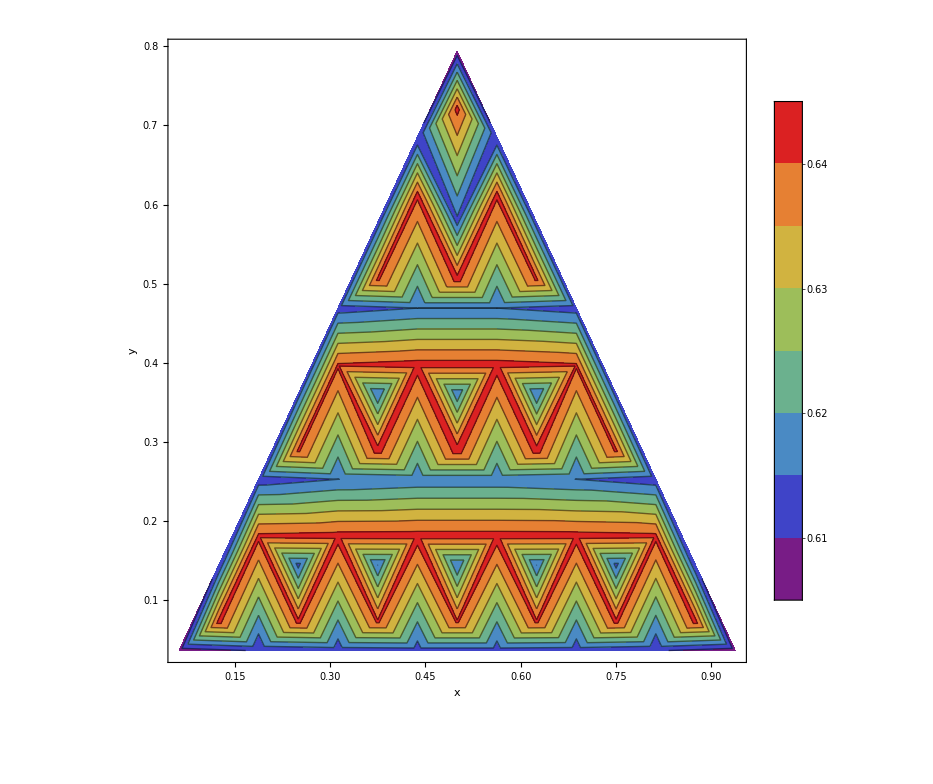

```mathematica
ListDensityPlot[Data,ColorFunction->"Rainbow",PlotLegends->True,FrameLabel->{"x","y"}]
```

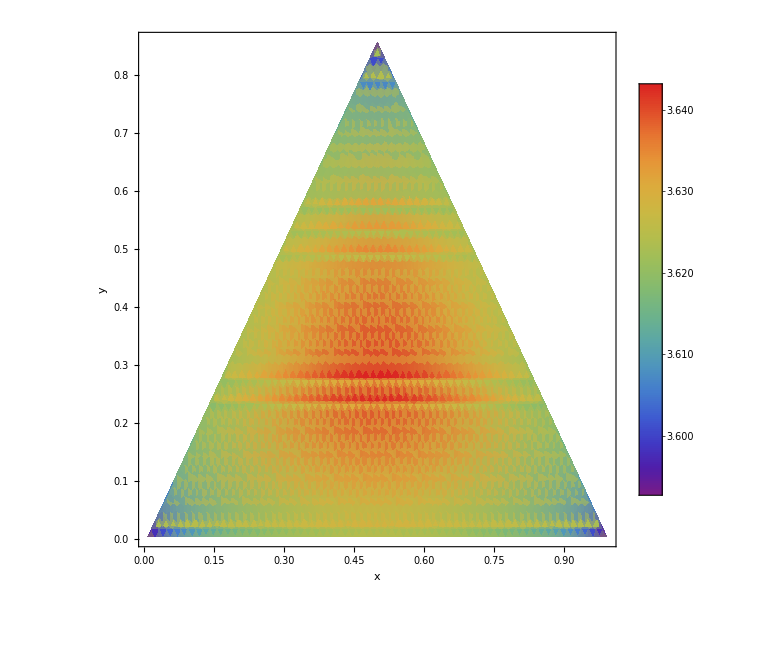

```mathematica
Data = Import["Perimeter.dat", "table"];
ListDensityPlot[Data,ColorFunction->"Rainbow",PlotLegends->True,FrameLabel->{"x","y"}]
```

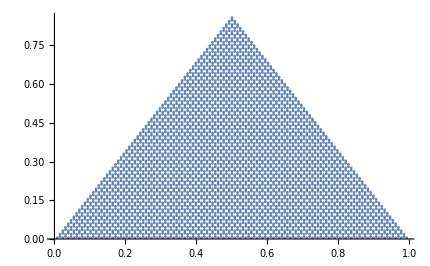

```mathematica
ListPlot[Data[[All, {1,2}]]]
```

```mathematica
Min[Data[[All, {1}]]]
```

0.0166

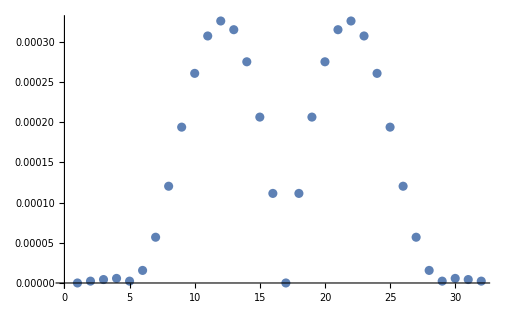

```mathematica
Diff = Norm/@(BData[[;;LB;;4]]-AData[[;;LA]]);
ListPlot[Diff]  (*Interesting Plot*)
```

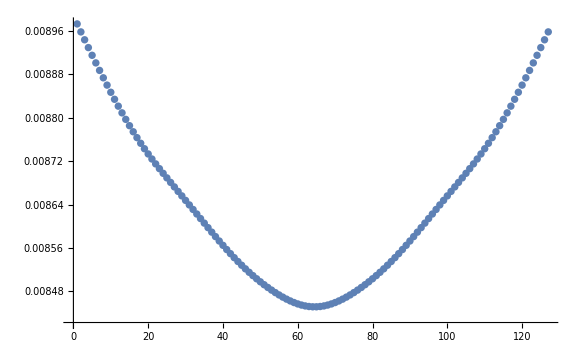

```mathematica
ListPlot[Norm/@(BData[[2;;LB]]-BData[[;;LB-1]])]
```

```mathematica
f1=Graphics3D[{Blue, PointSize[Medium], Point[AData]},Boxed->True, Axes->True];
f2=Graphics3D[{Red, PointSize[Medium], Point[BData]},Boxed->True, Axes->True];
Show[f1,f2]
```

-Graphics3D-

```mathematica
AData[[;;16]]
```

{{-0.525731,-0.303531,0.794655},{-0.463707,-0.31614,0.827666},{-0.400114,-0.327015,0.856137},{-0.335241,-0.336174,0.880114},{-0.26935,-0.343635,0.899648},{-0.202674,-0.349417,0.914785},{-0.135426,-0.353535,0.925566},{-0.0678048,-0.356001,0.932022},{0.,-0.356822,0.934172},{0.0678048,-0.356001,0.932022},{0.135426,-0.353535,0.925566},{0.202674,-0.349417,0.914785},{0.26935,-0.343635,0.899648},{0.335241,-0.336174,0.880114},{0.400114,-0.327015,0.856137},{0.463707,-0.31614,0.827666}}

```mathematica
BData[[;;32;;2]]
```

{{-0.525731,-0.303531,0.794654},{-0.463719,-0.316138,0.82766},{-0.400133,-0.327012,0.856129},{-0.335264,-0.336171,0.880106},{-0.269372,-0.343633,0.899642},{-0.202692,-0.349415,0.914781},{-0.135438,-0.353534,0.925565},{-0.0678108,-0.356001,0.932022},{0.,-0.356822,0.934172},{0.0678108,-0.356001,0.932022},{0.135438,-0.353534,0.925565},{0.202692,-0.349415,0.914781},{0.269372,-0.343633,0.899642},{0.335264,-0.336171,0.880106},{0.400133,-0.327012,0.856129},{0.463719,-0.316138,0.82766}}

```mathematica
Norm/@(BData[[;;32;;2]]-AData[[;;16]])
```

{3.125×10^-8,0.0000135491,0.0000212868,0.0000241888,0.000022882,0.0000185169,0.0000124604,6.10656×10^-6,4.41942×10^-8,6.10656×10^-6,0.0000124604,0.0000185169,0.000022882,0.0000241888,0.0000212868,0.0000135491}

```mathematica
ListPlot3D[AData,Mesh-> All, ViewPoint->{0,0,1}]
```

-Graphics3D-

```mathematica
ListPlot3D[BData,Mesh-> All, ViewPoint->{0,0,1}]
```

-Graphics3D-

```mathematica
Norm/@FinalData[[All, {3,4,5}]]
```

{80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624,80.2624}

```mathematica
fileset = Table[StringInsert["data/Triangleupdate_4_iter_.dat",ToString[i], -5], {i, nmax}];
```

```mathematica
dataSets = Table[Import[fileset[[i]]][[All, {3,4,5}]], {i,1, nmax, 10}];
```

```mathematica
plots=ListPlot3D[#,Mesh->All,  ViewPoint->{0,0,1}]&/@dataSets;
ListAnimate[plots]
```

```mathematica
Export["plots.mp4", plots,"FrameRate"->15]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

plots.mp4

```mathematica
data = Import["gd.txt", "table"][[;;-2]];
```

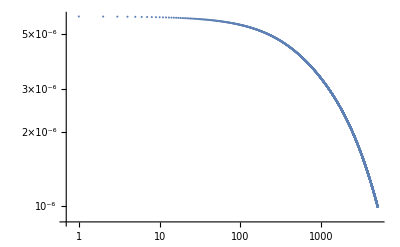

```mathematica
ListLogLogPlot[data[[All, {1,3}]]](*gradient*)
```

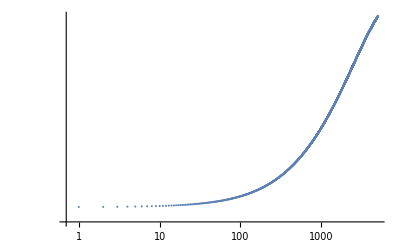

```mathematica
ListLogLogPlot[data[[All, {1,4}]]](*<A>*)
```

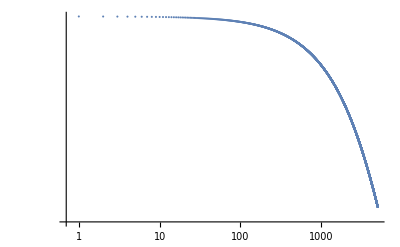

```mathematica
ListLogLogPlot[data[[All, {1,5}]]]
```

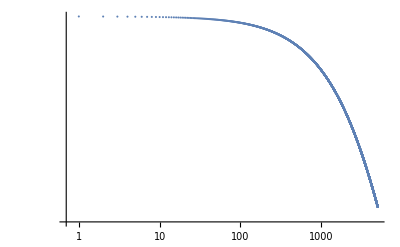

```mathematica
ListLogLogPlot[data[[All, {1,6}]]]
```

```mathematica
Action = data[[All, {7}]]+data[[All, {8}]]+data[[All, {9}]];
```

```mathematica
ActionTable=Table[Flatten[{data[[All, {1}]][[i]], Action[[i]]}, 1], {i, Length[Action]}];
```

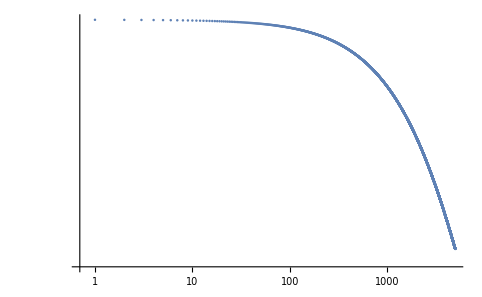

```mathematica
ListLogLogPlot[ActionTable]
```

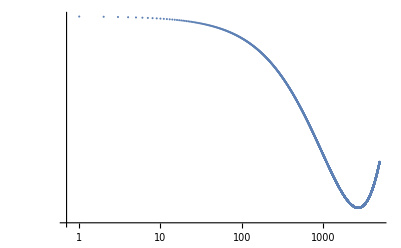

```mathematica
ListLogLogPlot[data[[All, {1,7}]]](*<A^2>*)
```

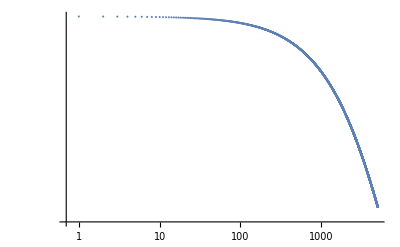

```mathematica
ListLogLogPlot[data[[All, {1,8}]]](*<P^2>*)
```

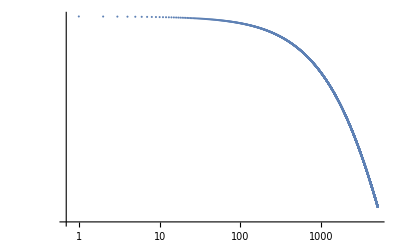

```mathematica
ListLogLogPlot[data[[All, {1,9}]]](*<P^2>*)
```

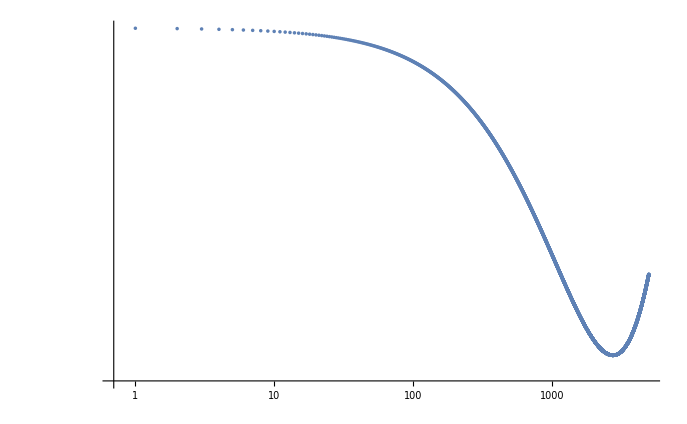

```mathematica
ListLogLogPlot[data[[All, {1,10}]]](*<RMS>*)
```

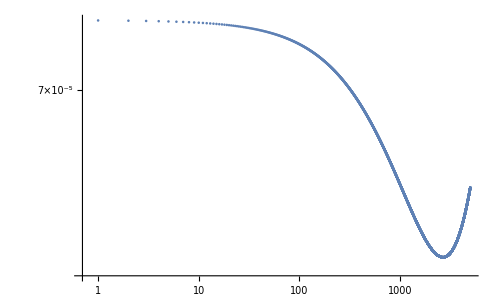

```mathematica
ListLogLogPlot[data[[2;;, {1,11}]]  ](*RMS*)
```

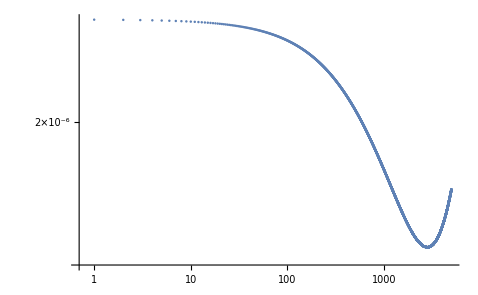

```mathematica
ListLogLogPlot[data[[2;;, {1,12}]]  ]
```

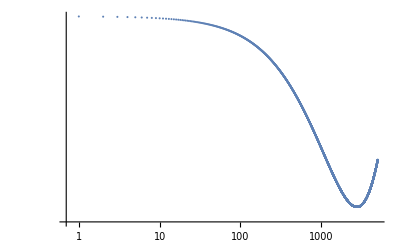

```mathematica
ListLogLogPlot[data[[2;;, {1,13}]]  ]
```

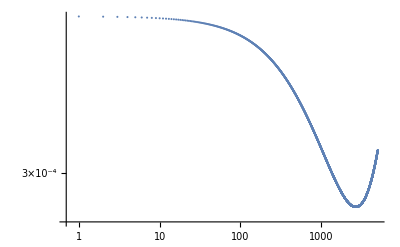

```mathematica
ListLogLogPlot[data[[2;;, {1,14}]]  ]
```

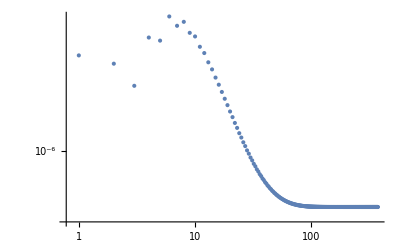

```mathematica
ListLogLogPlot[data[[2;;, {1,-1}]]]
```

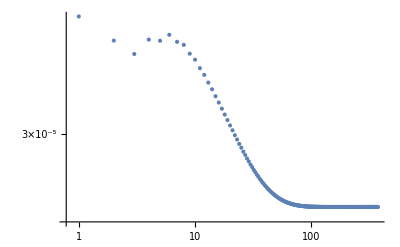

```mathematica
ListLogLogPlot[data[[2;;, {1,-2}]]]
```

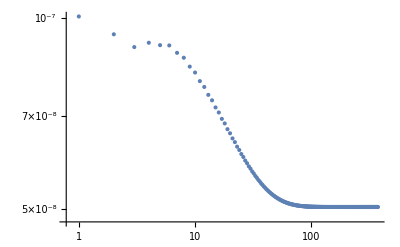

```mathematica
ListLogLogPlot[data[[2;;, {1,-3}]]]
```